# Espace ℝ^2

## Définition principale (Produit scalaire)

### Produit scalaire

```mathematica
⟨x_|y_⟩:=∑_(i=1)^Length[x] x[[i]]y[[i]]
```

## Autres définitions

### La norme

```mathematica
norm[x_]:=√⟨x|x⟩
```

### Normalization d’un vecteur

```mathematica
normalize[x_]:=x/(√⟨x|x⟩)
```

### Normalization d’un ensemble de vecteur

```mathematica
normalizeListe[vectors_]:=Table[normalize[vectors[[i]]],{i,1,Length[vectors]}]
```

### La projection orthogonale de y sur x

```mathematica
projection[y_,x_]:=⟨x|y⟩x/⟨x|x⟩
```

### Orthogonalisation (Gram–Schmidt algorithm)

```mathematica
gramSchmidt[vectors_]:=Module[{oVectors=vectors},
Do[oVectors[[i]]-=projection[oVectors[[i]],oVectors[[j]]],{i,2,Length[vectors]},{j,1,i-1}];
oVectors]
```

### Matrice d’orthonormalité

```mathematica
orthogonality[vectors_]:=Table[⟨vectors[[i]]|vectors[[j]]⟩,{i,1,Length[vectors]},{j,1,Length[vectors]}]//Simplify//TableForm
```

## Show

```mathematica
showVectors[vectors_]:=Graphics[{Blue,Map[Arrow[{{0,0},#}]&,vectors]},ImageSize->Small]
```

```mathematica
Project[a_,vectors_]:=Map[projection[a,#]&,vectors]
```

```mathematica
showProjections[a_,vectors_]:=Graphics[{Dashed,Red,Map[Arrow[{{0,0},#}]&,Project[a,vectors]]}]
```

```mathematica
showAll[a_,vectors_]:=Show[{showVectors[vectors],Graphics[{Red,Arrow[{{0,0},a}]}],showProjections[a,vectors]}]
```

## La base

### Base quelconque

La dimension de la base

```mathematica
dim:=2
```

```mathematica
baseQuelconque={{4,5},{3,5}}
```

{{4,5},{3,5}}

```mathematica
orthogonality[baseQuelconque]
```

41 | 37
37 | 34

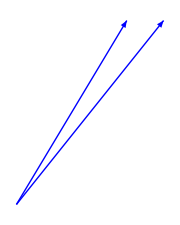

```mathematica
showVectors[baseQuelconque]
```

### Base orthogonale

```mathematica
baseOrthogonale=gramSchmidt[baseQuelconque]
```

{{4,5},{-25/41,20/41}}

```mathematica
orthogonality[baseOrthogonale]
```

41 | 0
0 | 25/41

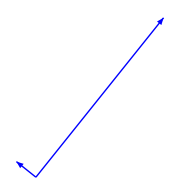

```mathematica
showVectors[baseOrthogonale]
```

### Base orthonormale

```mathematica
baseOrthonormale=normalizeListe[baseOrthogonale]//Simplify
```

{{4/(√41),5/(√41)},{-5/(√41),4/(√41)}}

```mathematica
orthogonality[baseOrthonormale]
```

1 | 0
0 | 1

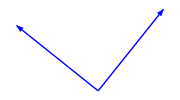

```mathematica
showVectors[baseOrthonormale]
```

## Développement du vecteur U sur une base

### Le vecteur à développer

```mathematica
U = {2,6};
```

### La base

```mathematica
RadioButtonBar[Dynamic[u],{baseQuelconque->"Base Quelconque",baseOrthogonale->"Base Orthogonale",baseOrthonormale->"Base Orthonormale"}]
```

| Base Quelconque   | Base Orthogonale   | Base Orthonormale

```mathematica
Dynamic[showAll[U,u]]
```

### Les coéfficients

```mathematica
Subscript[c, n_]:=⟨u[[n]]|U ⟩
```

```mathematica
Dynamic[Table[Subscript[c, n],{n,1,dim}]//Simplify]
```

### Développement

```mathematica
Dynamic[∑_(n=1)^dim Subscript[c, n] Subscript[𝓊, n]//Simplify]
```

```mathematica
adev=Dynamic[∑_(n=1)^dim Subscript[c, n] u[[n]]//Simplify]
```